# Two-loop on-shell vertex

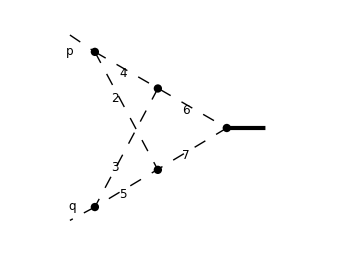
-Graphics-
(*The first entry in the basis, see below, is the irreducible numerator*)

## Search of the reduction rules and saving

#### Initialization

```mathematica
<<LiteRed`
SetDirectory[NotebookDirectory[]];
SetDim[d]
Declare[{l,r,p,q},Vector]
p·p=0;q·q=0;p·q=-1/2;
```

#### Defining the basis and searching for the symmetries & reduction rules

```mathematica
NewBasis[v2,{l-r,l,r,p-l,q-r,p-l+r,q-r+l},{l,r},Directory->"v2 dir"](*Basis definition. sp[l-r,l-r] is the irreducible numerator.*)
GenerateIBP[v2](*IBP generation. Can be also invoked by passing GenerateIBP->True option in NewBasis call*)
AnalyzeSectors[v2,{0,__}](*Zero and simple sectors determination. The second argument is a pattern which claims that the sectors with sp[p,r] in the denominator should not be analyzed*)
FindSymmetries[v2](*Finding unique and mapped sectors.*)
```

```mathematica
SetOptions[SolvejSector,Depth->0](*Depth->n is the option which determines the depth of the heuristtic search. The larger the depth, the more thorough is the search. But it also  takes longer.
If the search depth is not sufficient to reduce the sector to a finite number of integrals, the depth is increased automatically*)
SolvejSector/@UniqueSectors[v2](*Solving IBP identities for unique sectors.*)
DiskSave[v2](*Saving.*)
Quit[](*Quitting the kernel*)
```

## Loading the basis and reducing

```mathematica
<<LiteRed`
SetDirectory[NotebookDirectory[]];
<<"v2 dir/v2";
SetDim[d]
Declare[{l,r,p,q},Vector]
p·p=0;q·q=0;p·q=1/2;
IBPReduce[j[v2,-1,2,2,2,2,2,2]]
```

```mathematica
Timing[Collectj[IBPReduce[LoweringDRR[v2,0,1,1,1,1,1,1]],Factor]]
```

```mathematica
Timing[Collectj[IBPReduce[RaisingDRR[v2,0,1,1,1,1,1,1]],Factor]]
```